## Quantum (theory work)

P(τ_2,τ_3)=(i^3((2πℏ ω_F)/V))^3 π^2/(|aa'|)^2Exp[-2 σ_F^2(((3+4 σ_F^4(B_2^2+B_2 B_3+B_3^2))τ_2^2+(3+4 σ_F^4(B_1(B_2-B_3)+B_2(2 B_2+B_3)))τ_2 τ_3+(3+4 σ_F^4(B_2^2+B_2 B_1+B_1^2))τ_3^2)/(9+8σ_F^4[2(B_1^2+B_2^2+B_3^2)+B_1 B_2+B_2 B_3+B_3 B_1]+16 σ_F^8(B_1 B_2+B_2 B_3+B_3 B_1)^2))]
a=1/σF^2-ⅈ(B2+B3);
aprime=1/σF^2-ⅈ(B1+B3)-1/(4a)(1/σF^2-2ⅈB3)^2;
bprime=-ⅈ(A1-A3+t+τ-2/(4a)(1/σF^2-2ⅈB3)(A2-A3+τ));
cprime=1/(4a)(A2-A3+τ)^2+ⅈ ω0/3(2t+τ);
cnprime=cn((2πℏωF)/V)^(3/2)ⅇ^(ⅈ(Kf1+Kf2+Kf3-ω0t))√(π^2/aaprime);
Normalization:(π^2/Abs[(1/σFtest^2-ⅈ(B[2]+B[3]))(1/σFtest^2-ⅈ(B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ(B[2]+B[3]))))(1/σFtest^2-2ⅈ(B[3]))^2)])

## Quantum (code) (Analytical solution, approximated with narrowband filters)

```mathematica
Quantum[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=ⅇ^((2 σF^2 (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 t+4 A3 B1 B2 σF^4 t+8 A3 B2^2 σF^4 t-4 A3 B1 B3 σF^4 t+4 A3 B2 B3 σF^4 t-3 t^2-4 B2^2 σF^4 t^2-4 B2 B3 σF^4 t^2-4 B3^2 σF^4 t^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) t) τ-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 t-τ)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 t-B2 (B1+B3) τ-2 B2^2 (t+τ)+B3 (-2 B3 t+B1 τ)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (t-τ)+4 σF^4 (-2 B1^2 τ+B3 (2 B3 t+B2 (t+τ))-B1 (B3 (-t+τ)+B2 (t+τ))))))/(9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));
```

## Classical (theory work)

a_i^2 =1/(2 σF^2)-ⅈ B_i; 
E1 = E0/(2 √π a1)Exp[-((A1-t1)^2(1/(2 σF^2)+ⅈ B1))/(4((1/(2 σF^2))^2+B1^2))];
E2=E0/(2 √π a2)Exp[-((A2-(t1+t))^2(1/(2 σF^2) +ⅈ B2))/(4((1/(2 σF^2))^2+B2^2))];
E3=E0/(2 √π a3)Exp[-((A3-(t1+t+τ))^2(1/(2 σF^2) +ⅈ B3))/(4((1/(2 σF^2))^2+B3^2))];
I1 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B1^2))ⅇ^(-(A1-t1)^2/(2(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))));
I2 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B2^2))ⅇ^(-(A2-(t1+t))^2/(2(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))));
I3 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B3^2))ⅇ^(-(A3-(t1+t+τ))^2/(2(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))));
P[t_,τ_]=(η E0^6)/((2 √π)^6((1/(2 σF^2))^2+ B1^2)((1/(2 σF^2))^2+ B2^2)((1/(2 σF^2))^2+ B3^2))∫_(-∞)^∞ ⅇ^(-(A1-t1)^2/(2(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))))ⅇ^(-(A2-(t1+t))^2/(2(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))))ⅇ^(-(A3-(t1+t+τ))^2/(2(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))))ⅆt1

```mathematica
SimplifiedP=(ⅇ^(-(2 σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))) E0^6 η σF^11)/(π^(5/2) √((1+4 B1^2 σF^4) (1+4 B2^2 σF^4) (1+4 B3^2 σF^4) (3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))))
```

## Classical (code)

```mathematica
Classical[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=ⅇ^(-(2 σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4)));
```

## Analyzing variances of the quantum and the classical results

### Using ,⟨tτ⟩ for comparison

```mathematica
norm=∫_(-∞)^∞ ∫_(-∞)^∞ Classical[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

```mathematica
norm1[B1_,B2_,B3_]:=(471.23889803846896+0.1256637061435917 B3^2+B2^2 (0.1256637061435917+0.000025132741228718343 B3^2)+B1^2 (0.1256637061435917+0.000025132741228718343 B2^2+0.000025132741228718343 B3^2))/(√(0.75+0.0002000000000000001 B3^2+B2^2 (0.0002000000000000001+4.0000000000000034*^-8 B3^2)+B1^2 (0.0002000000000000001+4.0000000000000034*^-8 B2^2+4.0000000000000034*^-8 B3^2)))
```

```mathematica
res=∫_(-∞)^∞ ∫_(-∞)^∞ t τ Classical[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

#### Quantum case

We are calculating Norm=∫∫P_quantum(t,τ)ⅆtⅆτ

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ Quantum[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

$Aborted

Now, we are calculating =∫∫tτP_quantum(t,τ)ⅆtⅆτ

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ t τ ⅇ^(numer[0.1,t,τ,0,0,0,B1,B2,B3]/denom[0.1,t,τ,0,0,0,B1,B2,B3])ⅆtⅆτ
```

Taking the ratio gives ⟨tτ⟩ := qCov

```mathematica
qCov[B1_,B2_,B3_]:=(1/(3.7486824790711176*^11+6.664324407237545*^7 B3^2+B2^4 (17771.531752633462+1.7771531752633467 B3^2)+B2^2 (1.6660811018093863*^8+28878.73909802937 B3^2)+B2^3 (17771.531752633462 B3+0.8885765876316734 B3^3)+B2 (8.330405509046932*^7 B3+8885.765876316731 B3^3)+B1^3 (0.8885765876316734 B2^3-8885.765876316731 B3+0.8885765876316734 B2^2 B3-0.8885765876316734 B3^3+B2 (8885.765876316731-0.8885765876316734 B3^2))+B1^2 (6.664324407237545*^7+1.7771531752633467 B2^4+6.220036113421713 B2^3 B3+2221.4414690791823 B3^2+B2^2 (28878.73909802937+3.5543063505266934 B3^2)+B2 (22214.414690791826 B3-0.8885765876316734 B3^3))+B1 (-1.666081101809387*^7 B3+3.5543063505266934 B2^4 B3-8885.765876316731 B3^3+B2^3 (17771.531752633462+6.220036113421713 B3^2)+B2 (8.330405509046932*^7+22214.414690791826 B3^2)+B2^2 (22214.414690791826 B3+0.8885765876316734 B3^3)))/(2 √((23561.944901923438+3.141592653589793 B2^2+3.141592653589793 B2 B3+3.141592653589793 B3^2)/(5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))) √((6.714349161689327*^8-2.2617277734851675*^-15 B2^4+59683.10365946071 B2 B3-2.2617277734851675*^-15 B2^3 B3+119366.20731892143 B3^2+B2^2 (119366.20731892141+11.936620731892146 B3^2)+B1^2 (119366.20731892143+11.936620731892146 B2^2+23.873241463784296 B2 B3+11.936620731892146 B3^2)+B1 (-2.2617277734851675*^-15 B2^3+59683.103659460736 B3+23.873241463784296 B2^2 B3+B2 (59683.10365946071+23.873241463784296 B3^2)))/((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) (5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2))))) (4.2187499999999945*^11+7.499999999999994*^7 B3^2+B2^4 (19999.999999999993+2. B3^2)+B2^2 (1.8749999999999982*^8+32499.999999999985 B3^2)+B2^3 (19999.999999999993 B3+1. B3^3)+B2 (9.374999999999991*^7 B3+9999.999999999996 B3^3)+B1^3 (1. B2^3-9999.999999999996 B3+1. B2^2 B3-1. B3^3+B2 (9999.999999999996-1. B3^2))+B1^2 (7.499999999999994*^7+2. B2^4+7. B2^3 B3+2499.999999999998 B3^2+B2^2 (32499.999999999985+4. B3^2)+B2 (24999.99999999999 B3-1. B3^3))+B1 (-1.875*^7 B3+4. B2^4 B3-9999.999999999996 B3^3+B2^3 (19999.999999999993+7. B3^2)+B2 (9.374999999999991*^7+24999.99999999999 B3^2)+B2^2 (24999.999999999985 B3+1. B3^3)))))(-((0.00048367983046245834 (4.218749999999996*^11+8. B2^6+1.6874999999999985*^8 B2 B3+12.000000000000002 B2^5 B3+B2^4 (89999.99999999997+6.000000000000001 B3^2)+B2^2 (3.374999999999997*^8+22499.999999999993 B3^2)+B1^3 (1. B2^3-3.0000000000000004 B2^2 B3+3.0000000000000004 B2 B3^2-1. B3^3)+B2^3 (89999.99999999997 B3+1. B3^3)+B1^2 (22499.999999999993 B2^2+6.000000000000001 B2^4-44999.999999999985 B2 B3-9. B2^3 B3+22499.999999999993 B3^2+3.0000000000000004 B2 B3^3)+B1 (12.000000000000002 B2^5-1.6874999999999985*^8 B3+B2 (1.6874999999999985*^8-44999.999999999985 B3^2)+B2^3 (89999.99999999997-9. B3^2)+B2^2 (-44999.999999999985 B3-3.0000000000000004 B3^3))))/((7499.999999999997+1. B1 B2+2. B2^2-1. B1 B3+1. B2 B3)^2 (7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) √((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2)/(5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))) ((5.6249999999999955*^7-1.894780628693601*^-16 B2^4+4999.999999999998 B2 B3-1.894780628693601*^-16 B2^3 B3+9999.999999999998 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999998+1. B2^2+2.0000000000000004 B2 B3+1. B3^2)+B1 (-1.894780628693601*^-16 B2^3+5000. B3+2.0000000000000004 B2^2 B3+B2 (4999.999999999998+2.0000000000000004 B3^2)))/((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) (5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))))^(3/2))));
```

#### Classical case

```mathematica
cCov[B1_,B2_,B3_]:=-((0.0044546623974653695 (1.5624999999999975*^10+1.874999999999998*^7 B2^2+7499.999999999995 B2^4+1. B2^6) (1.8749999999999985*^7+4999.999999999998 B3^2+B2^2 (4999.999999999998+1. B3^2)+B1^2 (4999.999999999998+1. B2^2+1. B3^2))^2)/((2499.999999999999+1. B2^2)^2 (1.8749999999999985*^7-1.421085471520201*^-16 B2^4+4999.999999999998 B3^2+B2^2 (4999.999999999996+1. B3^2)+B1^2 (4999.999999999998+1. B2^2+1. B3^2)) √(5.8904862254808575*^7-4.46447167745105*^-16 B2^4+15707.96326794896 B3^2+B2^2 (15707.963267948955+3.141592653589793 B3^2)+B1^2 (15707.96326794896+3.141592653589793 B2^2+3.141592653589793 B3^2))))/((471.23889803846896+0.1256637061435917 B3^2+B2^2 (0.1256637061435917+0.000025132741228718343 B3^2)+B1^2 (0.1256637061435917+0.000025132741228718343 B2^2+0.000025132741228718343 B3^2))/(√(0.75+0.0002000000000000001 B3^2+B2^2 (0.0002000000000000001+4.0000000000000034*^-8 B3^2)+B1^2 (0.0002000000000000001+4.0000000000000034*^-8 B2^2+4.0000000000000034*^-8 B3^2))))
```

#### Comparing results

```mathematica
cCov[10,-20,-30]
```

-58.

```mathematica
qCov[100,-200,-300]
```

-1050.

```mathematica
FindArgMin[Abs[qCov[10,-20,z]],z]
```

FindArgMin::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{270.012}

### Using SVD for comparison

#### For σF=0.1, B1=10, B2=20,B3=30,Range=50

```mathematica
σFtest=0.5;
B[1]=10;
B[2]=20;
B[3]=30;
range=50;
clas=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
clas=clas/Total[Total[clas]];
quan=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quan=quan/Total[Total[quan]];
```

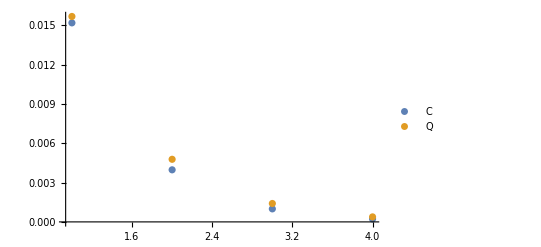

```mathematica
{uc,wc,vc}=SingularValueDecomposition[clas];
{uq,wq,vq}=SingularValueDecomposition[quan];
ListPlot[{Part[Diagonal[wc],1;;4],Part[Diagonal[wq],1;;4]},PlotLegends-> {"C","Q"},PlotRange->All]
```

```mathematica
plot1=ListContourPlot[uq.wq.DiagonalMatrix[{1,1},0,Dimensions[wq][[1]]].vq†,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"quantum",PlotRange->Full,Contours->5,ImageSize->Scaled[0.25]];
plot2=ListContourPlot[uc.wc.DiagonalMatrix[{1,1},0,Dimensions[wc][[1]]].vc†,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"classical",PlotRange->Full,Contours->5,ImageSize->Scaled[0.25]];
GraphicsRow[{plot1,plot2},ImageSize->Scaled[0.25]]
```

-Graphics-

## Plots

We map all the results from analytical as well numerical solutions into matrices of dimension (2 range+1)x(2 range +1) where x and y axis in the plots go from (-range, range).

```mathematica
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
```

### Experiment 0

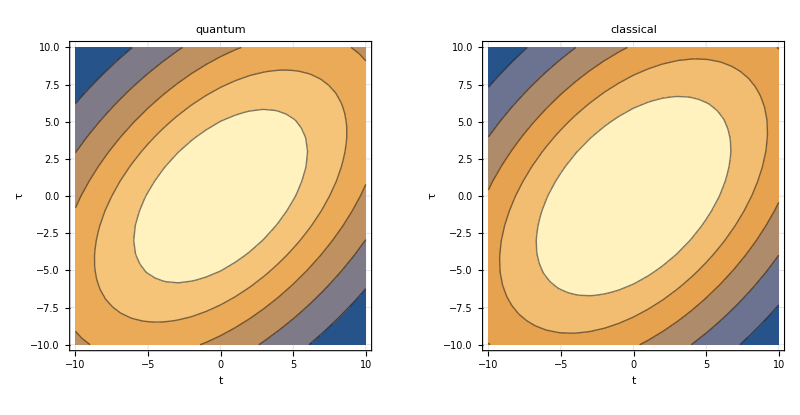

```mathematica
range=10;
σFtest=0.1;
B[1]=10;
B[2]=-20;
B[3]=20;
classical0=Table[N[Classical[σFtest,t-range -1,τ-t,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical0=classical0/Total[Total[classical0]];
quanalytical0=Table[N[Quantum[0.1,t-range -1,τ-t,0,0,0,B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical0=quanalytical0/Total[Total[quanalytical0]];
plot1=ListContourPlot[classical0,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"classical",PlotRange->Full,Contours-> 5,ImageSize->Scaled[1]];
plot2=ListContourPlot[quanalytical0,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"quantum",PlotRange->Full,Contours-> 5,ImageSize->Scaled[1]];
GraphicsRow[{plot2,plot1}]
```

```mathematica
ratioτ=quanalytical0[[0+range+1,1+range+1]]/classical0[[0+range+1,1+range+1]]
```

0.97709

```mathematica
ratiot=classical0[[1+range+1,0+range+1]]/quanalytical0[[1+range+1,0+range+1]]
```

0.977398

### Experiment 1: Range = -10, 10, B1=10, B2=-20, B3=-30,σF =0.5

```mathematica
range=10;
B[1]=10;
B[2]=20;
B[3]=30;
σFtest=0.5;
```

Classical

```mathematica
classical1=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical1=classical1/Total[Total[classical1]];
```

Quantum (analytical solution)

```mathematica
quanalytical1=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical1=quanalytical1/Total[Total[quanalytical1]];
```

For Quantum (numerical solution), we directly create the matrix. This is time consuming so we use get values in upper half and simply use those results in the lower half after inversion along the y-axis. We only do this because the plots are symmetrical.  
The code outputs the current value of (t,τ) at which the function is being calculated.

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
ClearAll[int2,result2]
Do[
Do[
int2[t,τ][ω1_,ω2_,ω3_,t1_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t1 -ω2 (t1+t)-ω3 (t1+t+τ))],
{t,-range,range,1}
],{τ,-range,range,1}
]
Monitor[Do[
Do[
result2[t,τ]=NIntegrate[int2[t,τ][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result2[-t,-τ]=result2[t,τ]
,{t,-range,range,1}],{τ,0,range,1}],{t,τ}]
qunumerical1=Table[Abs[result2[t-range -1,τ-range -1]]^2,{t,1,2 range +1},{τ,1,2 range +1}];
qunumerical1 = qunumerical1/Total[Total[qunumerical1]];
```

Plotting

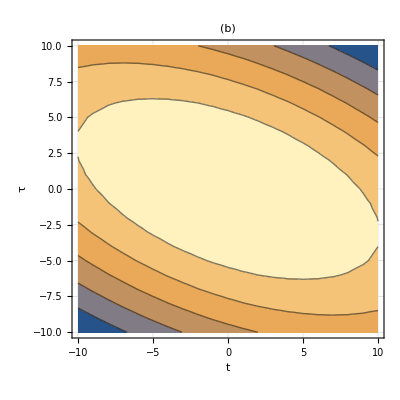

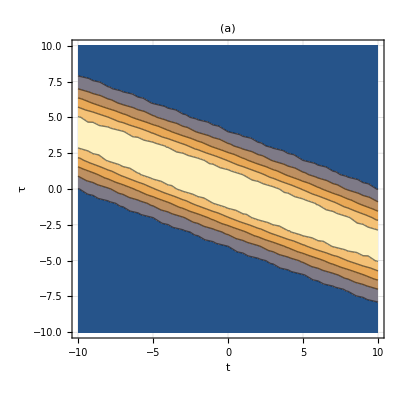

```mathematica
ListContourPlot[classical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

```mathematica
ListContourPlot[qunumerical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

### Experiment 2: Range = -10, 10, B1=10, B2=+20, B3=+30,σF =0.5

```mathematica
range=10;
B[1]=10;
B[2]=20;
B[3]=30;
σFtest=0.5;
```

Classical

```mathematica
classical2=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical2=classical2/Total[Total[classical2]];
```

Quantum (analytical solution)

```mathematica
quanalytical2=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical2=quanalytical2/Total[Total[quanalytical2]];
```

For Quantum (numerical solution), we directly create the matrix. This is time consuming so we use get values in upper half and simply use those results in the lower half after inversion along the y-axis. We only do this because the plots are symmetrical.  
The code outputs the current value of (t,τ) at which the function is being calculated.

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
ClearAll[int2,result2]
Do[
Do[
int2[t,τ][ω1_,ω2_,ω3_,t1_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t1 -ω2 (t1+t)-ω3 (t1+t+τ))],
{t,-range,range,1}
],{τ,-range,range,1}
]
Monitor[Do[
Do[
result2[t,τ]=NIntegrate[int2[t,τ][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result2[-t,-τ]=result2[t,τ]
,{t,-range,range,1}],{τ,0,range,1}],{t,τ}]
qunumerical2=Table[Abs[result2[t-range -1,τ-range -1]]^2,{t,1,2 range +1},{τ,1,2 range +1}];
qunumerical2= qunumerical2/Total[Total[qunumerical2]];
```

Plotting

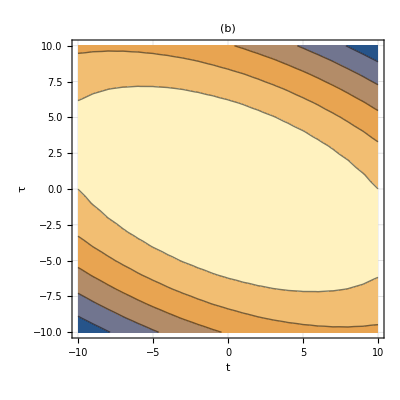

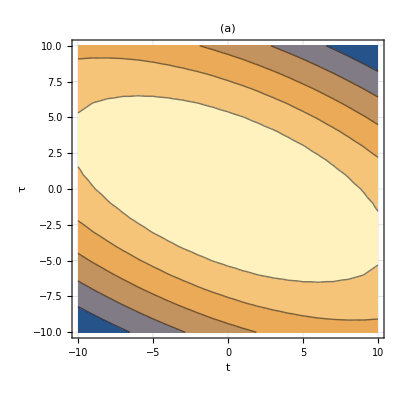

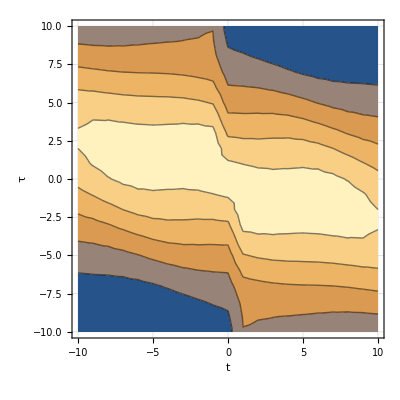

```mathematica
ListContourPlot[classical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
ListContourPlot[qunumerical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 3: Range = (-500, 500), B1=-150, B2=-150, B3=300,σF =0.1

```mathematica
range=100;
B[1]=-150;
B[2]=-150;
B[3]=300;
σFtest=0.1;
```

Classical

```mathematica
classical3=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical3=classical3/Total[Total[classical3]];
```

Quantum (analytical solution)

```mathematica
quanalytical3=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical3=quanalytical3/Total[Total[quanalytical3]];
```

Plotting

```mathematica
ListContourPlot[classical3,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical3,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

-Graphics-

### Experiment 4: Range = (-50, 50), B1=-15, B2=-15, B3=30,σF =0.1

```mathematica
range=50;
B[1]=-15;
B[2]=-15;
B[3]=30;
σFtest=0.1;
```

Classical

```mathematica
classical4=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical4=classical4/Total[Total[classical4]];
```

Quantum (analytical solution)

```mathematica
quanalytical4=(π^2/Abs[(1/σFtest^2-ⅈ (B[2]+B[3])) (1/σFtest^2-ⅈ (B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ (B[2]+B[3]))))(1/σFtest^2-2ⅈ (B[3]))^2)])Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical4=quanalytical4/Total[Total[quanalytical4]];
```

Plotting

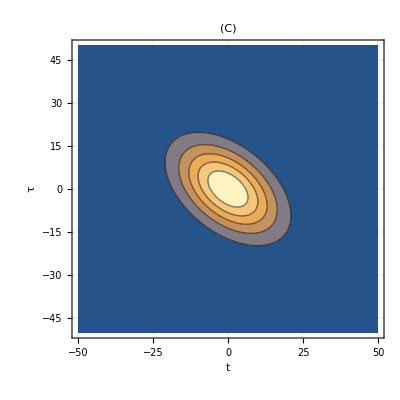

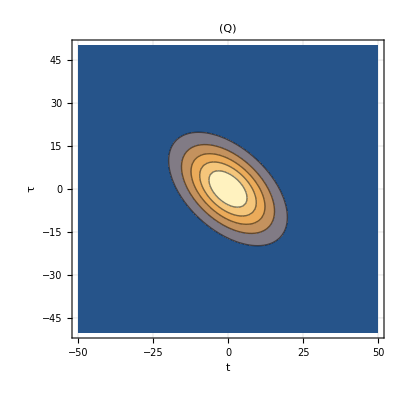

```mathematica
ListContourPlot[classical4,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical4,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 5: Range = (-50, 50), B1=10, B2=-20, B3=-30,σF =0.5

```mathematica
ClearAll[classical5,quanalytical5,range,σFtest,B]
range=50;
B[1]=10;
B[2]=-20;
B[3]=-30;
σFtest=0.5;
```

Classical

```mathematica
classical5=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical5=classical5/Total[Total[classical5]];
```

Quantum (analytical solution)

```mathematica
quanalytical5=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical5=quanalytical5/Total[Total[quanalytical5]];
```

Plotting

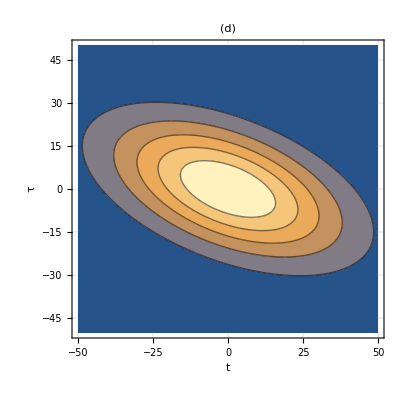

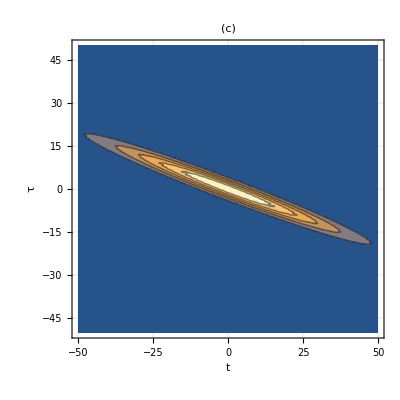

```mathematica
ListContourPlot[classical5,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(d)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical5,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(c)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 6: Range = (-50, 50), B1=10, B2=10, B3=10,σF =0.1

```mathematica
range=50;
B[1]=10;
B[2]=10;
B[3]=10;
σFtest=0.1;
```

Classical

```mathematica
classical6=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical6=classical6/Total[Total[classical6]];
```

Quantum (analytical solution)

```mathematica
quanalytical6=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical6=quanalytical6/Total[Total[quanalytical6]];
```

Plotting

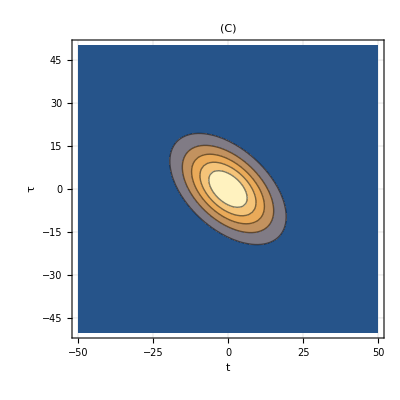

-Graphics-

```mathematica
ListContourPlot[classical6,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical6,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 7: Range = (-50, 50), B1=-15, B2=30, B3=-15,σF =0.1

```mathematica
range=50;
B[1]=-15;
B[2]=30;
B[3]=-15;
σFtest=0.1;
```

Classical

```mathematica
classical7=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical7=classical7/Total[Total[classical7]];
```

Quantum (analytical solution)

```mathematica
quanalytical7=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical7=quanalytical7/Total[Total[quanalytical7]];
```

Plotting

```mathematica
ListContourPlot[classical7,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical7,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

-Graphics-

### Experiment 8: Range = (-50, 50), B1=30, B2=-15, B3=-15,σF =0.1

```mathematica
range=50;
B[1]=30;
B[2]=-15;
B[3]=-15;
σFtest=0.1;
```

Classical

```mathematica
classical8=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical8=classical8/Total[Total[classical8]];
```

Quantum (analytical solution)

```mathematica
quanalytical8=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical8=quanalytical8/Total[Total[quanalytical8]];
```

Plotting

```mathematica
ListContourPlot[classical8,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical8,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

-Graphics-

### Experiment 9: Range = (-50, 50), B1=30, B2=-15, B3=-15,σF =0.3

```mathematica
range=50;
B[1]=-15;
B[2]=-15;
B[3]=30;
σFtest=0.3;
```

Classical

```mathematica
classical9=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical9=classical9/Total[Total[classical9]];
```

Quantum (analytical solution)

```mathematica
quanalytical9=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical9=quanalytical9/Total[Total[quanalytical9]];
```

Plotting

```mathematica
ListContourPlot[classical9,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical9,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

-Graphics-

### Experiment Z: Range: 50, Manipulate B_i

```mathematica
Manipulate[
range=50;
σFtest=0.1;
classicalZ=Table[N[Classical[σFtest,t-range -1,τ-range -1,0,0,0,b1,b2,b3]],{t,1,2 range +1},{τ,1,2 range +1}];
classicalZ=classicalZ/Total[Total[classicalZ]];
quantumZ=Table[N[Quantum[σFtest,t-range -1,τ-range -1,0,0,0,b1,b2,b3]],{t,1,2 range +1},{τ,1,2 range +1}];
quantumZ=quantumZ/Total[Total[quantumZ]];
plt1=ListContourPlot[quantumZ,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->25,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(Q)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]];
plt2=ListContourPlot[classicalZ,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->25,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(C)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]];
GraphicsRow[{p1,p2},ImageSize-> Scaled[0.5]],{b1,-30,30,5,Appearance-> "Open"},{b2,-30,30,5,Appearance-> "Open"},{b3,-30,30,5,Appearance-> "Open"}]
```

## Final plots v2

```mathematica
range=50;
σFtest=0.1;
B[1,1]=0;
B[2,1]=0;
B[3,1]=0;
B[1,2]=-25;
B[3,2]=-25;
B[2,2]=50;
B[1,3]=-100;
B[3,3]=-100;
B[2,3]=200;
B[1,4]=-1000;
B[3,4]=-1000;
B[2,4]=2000;
ClearAll[p1,p2]
Do[
classical[i]=Table[N[Classical[σFtest,t-range -1,τ-range -1,0,0,0,B[1,i],B[2,i],B[3,i]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical[i]=classical[i]/Total[Total[classical[i]]];
quantum[i]=Table[N[Quantum[σFtest,t-range -1,τ-range -1,0,0,0,B[1,i],B[2,i],B[3,i]]],{t,1,2 range +1},{τ,1,2 range +1}];
quantum[i]=quantum[i]/Total[Total[quantum[i]]];
p1[i]=ListContourPlot[quantum[i],DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,95+2i,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True];
p2[i]=ListContourPlot[classical[i],DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,96+2i,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True],
{i,1,3}]
(*finalPlot=GraphicsGrid[{{p1[1],p2[1]},{p1[2],p2[2]},{p1[3],p2[3]},{p1[4],p2[4]}},ImageSize->Scaled[0.75]]*)
```

```mathematica
newrange=500;
classical[4]=Table[N[Classical[σFtest,t-newrange -1,τ-newrange -1,0,0,0,B[1,4],B[2,4],B[3,4]]],{t,1,2 newrange +1},{τ,1,2 newrange +1}];
classical[4]=classical[4]/Total[Total[classical[4]]];
quantum[4]=Table[N[Quantum[σFtest,t-newrange -1,τ-newrange -1,0,0,0,B[1,4],B[2,4],B[3,4]]],{t,1,2 newrange +1},{τ,1,2 newrange +1}];
quantum[4]=quantum[4]/Total[Total[quantum[4]]];
range=50;
p1[4]=ListContourPlot[quantum[4][[newrange+1-range;;newrange+1+range,newrange+1-range;;newrange+1+range]],DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,95+2 4,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True];
p2[4]=ListContourPlot[classical[4][[newrange+1-range;;newrange+1+range,newrange+1-range;;newrange+1+range]],DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,96+2 4,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True];
```

```mathematica
finalPlot=GraphicsGrid[{{p1[1],p2[1]},{p1[2],p2[2]},{p1[3],p2[3]},{p1[4],p2[4]}},ImageSize->Scaled[0.75]]
```

-Graphics-

## Model fitting

```mathematica
model=a Exp[(-(Cos[ϕ]^2(Cos[θ]t-Sin[θ]τ)^2+Sin[ϕ]^2(Sin[θ]t+Cos[θ]τ)^2))/(2 σ^2)];
Do[
range =(Dimensions[classical[k]][[1]]-1)/2;
cIdxData[k]= Table[{i-range -1,j-range-1,classical[k][[i,j]]},{i,1,2range+1},{j,1,2range+1}];
cData[k]=Flatten[cIdxData[k],1];
cfit[k] = FindFit[cData[k],model,{{a,0.5},σ,θ,ϕ},{t,τ}];
qIdxData[k]= Table[{i-range -1,j-range-1,quantum[k][[i,j]]},{i,1,2range+1},{j,1,2range+1}];
qData[k]=Flatten[qIdxData[k],1];
qfit[k] = FindFit[qData[k],model,{{a,0.5},σ,θ,ϕ},{t,τ}],
  {k,1,4}]
```

Comparing (a) and (b), the cases with B1 = B2 = B3 = 0

```mathematica
qfit[1]
```

{a→0.00183776,σ→6.12372,θ→0.785398,ϕ→1.0472}

```mathematica
cfit[1]
```

{a→0.00183776,σ→6.12372,θ→0.785398,ϕ→1.0472}

Comparing (c) and (d), the cases with B1 =-25, B2 =-25, B3 =+5 0

```mathematica
qfit[2]
```

{a→0.00147023,σ→6.84653,θ→0.785398,ϕ→2.0944}

```mathematica
cfit[2]
```

{a→0.00124265,σ→7.55415,θ→0.931127,ϕ→2.12061}

Comparing (e) and (f), the cases with B1 =-100, B2 =-100, B3 =+200

```mathematica
qfit[3]
```

{a→0.00038467,σ→13.6931,θ→0.785398,ϕ→2.0944}

```mathematica
cfit[3]
```

{a→0.000266816,σ→17.4553,θ→1.22343,ϕ→2.10122}

Comparing (g) and (h), the cases with B1 =-1000, B2 =-1000, B3 =+2000

```mathematica
qfit[4]
```

{a→4.69343×10^-6,σ→122.627,θ→0.785398,ϕ→2.0944}

```mathematica
cfit[4]
```

{a→3.02001×10^-6,σ→160.509,θ→1.27622,ϕ→1.05575}

## Table of σ parameters of the fits (First column is for quantum results, Second column for the corresponding classical results)

```mathematica
MatrixForm[Table[{qfit[i][[2,2]],cfit[i][[2,2]]},{i,1,4}]]
```

(6.12372 | 6.12372
6.84653 | 7.55415
13.6931 | 17.4553
122.627 | 160.509)

## Check: Plotting fit and the original data

```mathematica
Show[Plot3D[model/.qfit[2],{t,-range,range},{τ,-range,range},PlotRange->All,PlotPoints->2 range+1],ListPointPlot3D[qData[2],PlotStyle->Directive[PointSize[Small],Red]]]
```

General::munfl: Exp[-3999.98] is too small to represent as a normalized machine number; precision may be lost.

$Aborted